```mathematica
testFileName = "/Users/chengling/Downloads/bd_N1024_p3.75000_T0.00055000_t100000.000000_1.nc";
```

```mathematica
Import[testFileName,"Datasets"]
```

{position,velocity,type,additionalData,BoxMatrix,time,meanQ}

```mathematica
{position,velocity,type,additionalData,boxMatrix,time,meanQ}=Import[testFileName,"Data"];
```

```mathematica
readFile[foretxt_,index_]:=Module[{position,velocity,type,additionalData,boxMatrix,time},
{position,velocity,type,additionalData,boxMatrix,time,meanQ}=Import[StringJoin[foretxt,ToString[index],".nc"],"Data"];
{position,boxMatrix}]
```

```mathematica
DIM=2;
boxInvTrans[boxmat_,pt_]:=Module[{invmat},
invmat=Inverse[boxmat];
invmat.pt
];
boxTrans[boxmat_,pt_]:=boxmat.pt;
putInBox[boxmat_,pt_]:=Module[{temp},
temp=boxInvTrans[boxmat,pt];
Do[
If[Between[temp[[dd]]==False,{0,1}],temp[[dd]]-=Sign[temp[[dd]]]];
,{dd,1,DIM}];
boxTrans[boxmat,temp]
];
minDist[boxmat_,ptA_,ptB_]:=Module[{vA,vB,disp},
vA=boxInvTrans[boxmat,ptA];
vB=boxInvTrans[boxmat,ptB];
disp=vA-vB;
Do[
If[Abs[disp[[dd]]]>0.5,disp[[dd]]-=Sign[disp[[dd]]]];
,{dd,1,DIM}];
boxTrans[boxmat,disp]
];
overlapCri=Sqrt[(4/3)/(1+0.5*1/3)]/2
```

```mathematica
overlapCri
```

0.534522

```mathematica
overlapFunction[d_]:=If[d>overlapCri,0,1]
computeOverlap[inipts_,pts_,boxmat_]:=Module[{minDists,minLenths,overlaps},
minDists=Table[minDist[boxmat,inipts[[i]],pts[[i]]],{i,1,Length[pts]}];
minLenths=Table[Sqrt[minDists[[i,1]]^2+minDists[[i,2]]^2],{i,1,Length[pts]}];
overlaps= Table[overlapFunction[minLenths[[i]]],{i,1,Length[pts]}];
Total[overlaps]/Length[pts]
];
computeOverlapLarge[inipts_,pts_,boxmat_]:=Module[{minDists,minLenths,overlaps},
minDists=Table[minDist[boxmat,inipts[[i]],pts[[i]]],{i,1,Length[pts]/2}];
minLenths=Table[Sqrt[minDists[[i,1]]^2+minDists[[i,2]]^2],{i,1,Length[pts]/2}];
overlaps= Table[overlapFunction[minLenths[[i]]],{i,1,Length[pts]/2}];
Total[overlaps]/Length[pts]*2
]
```

```mathematica
Length[Partition[position[[1]],2]]/2
```

512

```mathematica
LowT=Table[{position,boxMatrix}=readFile["/Users/chengling/Downloads/bd_N1024_p3.75000_T0.00055000_t100000.000000_",j];
Table[N[computeOverlap[Partition[position[[1]],2],Partition[position[[i]],2],Partition[boxMatrix[[i]],2]]],{i,1,Length[position]}],{j,1,10}];
```

```mathematica
HighT=Table[{position,boxMatrix}=readFile["/Users/chengling/Downloads/bd_N1024_p3.75000_T0.15000000_t100000.000000_",j];
Table[N[computeOverlap[Partition[position[[1]],2],Partition[position[[i]],2],Partition[boxMatrix[[i]],2]]],{i,1,Length[position]}],{j,1,10}];
```

```mathematica
ListHighT=Table[{Log10[time[[i]]-10000][[1]],(Mean/@Transpose[HighT])[[i]]},{i,1,40}];
```

```mathematica
ListLowT=Table[{Log10[time[[i]]-10000][[1]],(Mean/@Transpose[LowT])[[i]]},{i,1,40}];
```

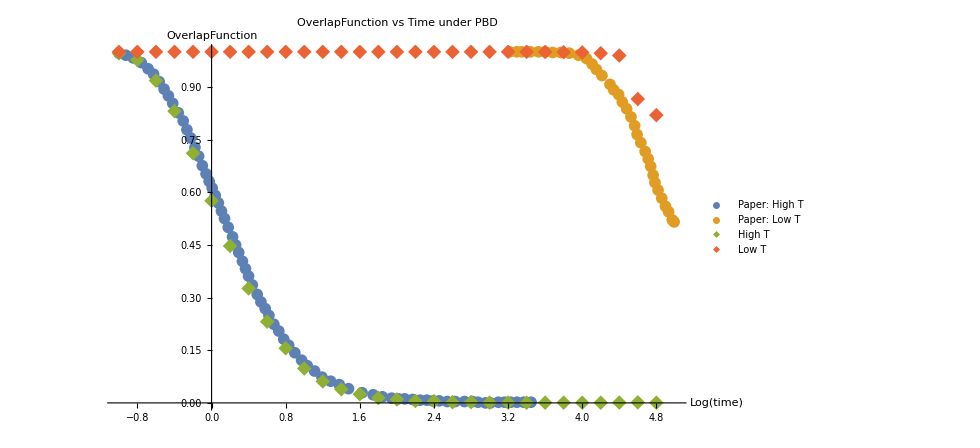

```mathematica
PBQT=ListPlot[{paperHighT,paperLowT,ListHighT,ListLowT},PlotLegends->{"Paper: High T","Paper: Low T", "High T","Low T"},PlotMarkers->{{"●",12},{"●",12},{"◆",15},{"◆",15}},
PlotLabel->"OverlapFunction vs Time under PBD",AxesLabel->{"Log(time)","OverlapFunction"},
PlotRange->{{-1,5},Automatic}]
```

```mathematica
LowTLarge=Table[{position,boxMatrix}=readFile["/Users/chengling/Downloads/bd_N1024_p3.75000_T0.00055000_t100000.000000_",j];
Table[N[computeOverlapLarge[Partition[position[[1]],2],Partition[position[[i]],2],Partition[boxMatrix[[i]],2]]],{i,1,Length[position]}],{j,1,10}];
```

```mathematica
HighTLarge=Table[{position,boxMatrix}=readFile["/Users/chengling/Downloads/bd_N1024_p3.75000_T0.15000000_t100000.000000_",j];
Table[N[computeOverlapLarge[Partition[position[[1]],2],Partition[position[[i]],2],Partition[boxMatrix[[i]],2]]],{i,1,Length[position]}],{j,1,10}];
```

```mathematica
ListHighTLarge=Table[{Log10[time[[i]]-10000][[1]],(Mean/@Transpose[HighTLarge])[[i]]},{i,1,40}];
ListLowTLarge=Table[{Log10[time[[i]]-10000][[1]],(Mean/@Transpose[LowTLarge])[[i]]},{i,1,40}];
```

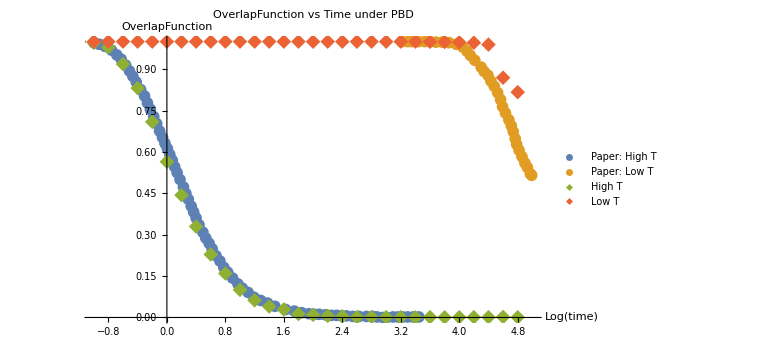

```mathematica
PBQT=ListPlot[{paperHighT,paperLowT,ListHighTLarge,ListLowTLarge},PlotLegends->{"Paper: High T","Paper: Low T", "High T","Low T"},PlotMarkers->{{"●",12},{"●",12},{"◆",15},{"◆",15}},
PlotLabel->"OverlapFunction vs Time under PBD",AxesLabel->{"Log(time)","OverlapFunction"},
PlotRange->{{-1,5},Automatic}]
```

```mathematica
LowT[[1]]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.995117,1.,0.995117,0.604492,0.0546875,0.0585938}

```mathematica
LowTLarge[[1]]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.994141,1.,0.996094,0.599609,0.0585938,0.0625}

```mathematica
ListHighT
```

{{-5.80175,1.},{-2.69863,1.},{-2.52265,1.},{-2.39777,1.},{-2.22173,1.},{-1.99993,1.},{-1.79584,1.},{-1.60203,1.},{-1.39792,0.999414},{-1.20065,0.996094},{-0.999993,0.981348},{-0.801339,0.94541},{-0.600324,0.884766},{-0.400115,0.81582},{-0.19997,0.733789},{6.85629×10^-7,0.64707},{0.20003,0.554785},{0.40002,0.462793},{0.599992,0.38623},{0.800029,0.312402},{1.,0.254492},{1.2,0.200879},{1.4,0.161133},{1.6,0.128223},{1.8,0.0958984},{2.,0.0792969},{2.2,0.0632813},{2.4,0.0536133},{2.6,0.0382813},{2.8,0.0329102},{3.,0.0239258},{3.2,0.022168},{3.4,0.0254883},{3.6,0.0243164},{3.8,0.022168},{4.,0.0220703},{4.2,0.0203125},{4.4,0.0268555},{4.6,0.0250977},{4.8,0.0264648}}

```mathematica
ListHighTLarge
```

{{-5.80175,1.},{-2.69863,1.},{-2.52265,1.},{-2.39777,1.},{-2.22173,1.},{-1.99993,1.},{-1.79584,1.},{-1.60203,1.},{-1.39792,0.999414},{-1.20065,0.99668},{-0.999993,0.980664},{-0.801339,0.946094},{-0.600324,0.883789},{-0.400115,0.812109},{-0.19997,0.728516},{6.85629×10^-7,0.643359},{0.20003,0.549219},{0.40002,0.466406},{0.599992,0.3875},{0.800029,0.310156},{1.,0.257813},{1.2,0.204297},{1.4,0.16543},{1.6,0.132617},{1.8,0.0964844},{2.,0.0757813},{2.2,0.0683594},{2.4,0.0556641},{2.6,0.0376953},{2.8,0.0347656},{3.,0.0224609},{3.2,0.0236328},{3.4,0.0251953},{3.6,0.0251953},{3.8,0.0244141},{4.,0.0220703},{4.2,0.0197266},{4.4,0.0285156},{4.6,0.0261719},{4.8,0.0269531}}